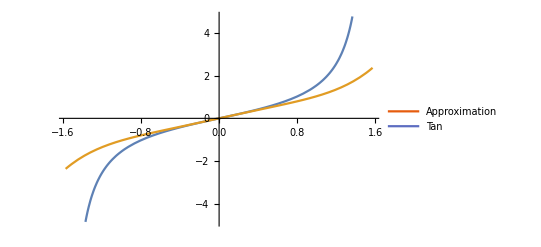

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],x + x^3 (1/3 - 4/Pi^2) + x^5 (2/15 - 4/(5 * 4 * Pi^2))},{x, -Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```

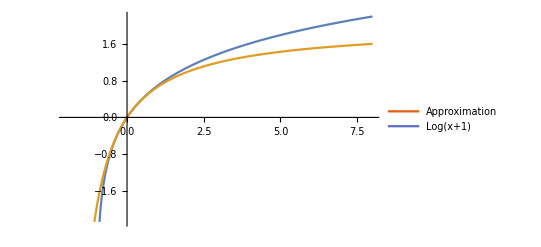

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Log(x+1)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Log[x + 1],x /(1 + x/2)},{x,-2 ,8},PlotLegends->leg,ImageSize->400]
```

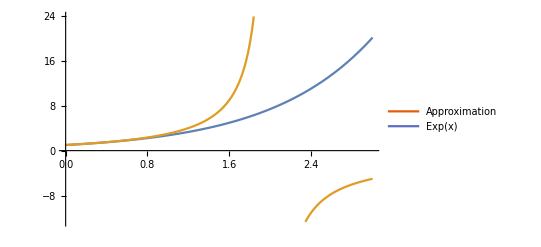

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Exp(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Exp[x],(1 + x/2)/(1 - x/2)},{x,0,3},PlotLegends->leg,ImageSize->400]
```

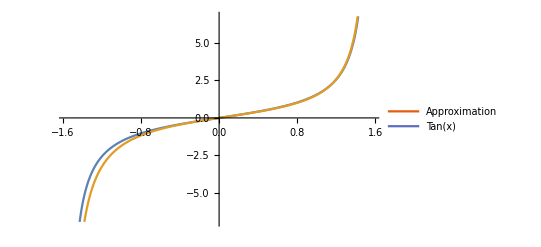

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],(x)/((1 - 4 / Pi^2 * x ^2)*(1 + x * (1/2 - 4/Pi^2) ))},{x,-Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```

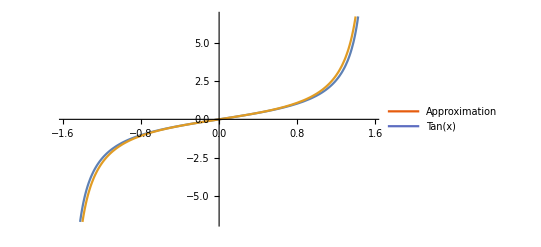

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],(x)/((1 - 4 / Pi^2 * x ^2)*(1 + x * (1/Pi + 1/12 - 4/Pi^2) ))},{x,-Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```

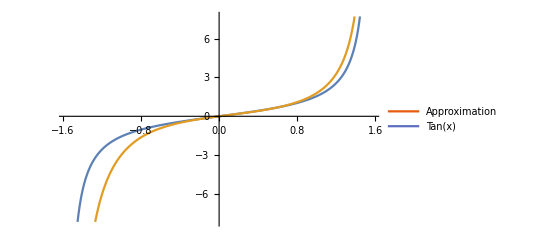

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],(x+ x^3/3)/((1 - 4 / Pi^2 * x ^2)*(1 + x * (1/Pi + 1/3 - 4/Pi^2) ))},{x,-Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```

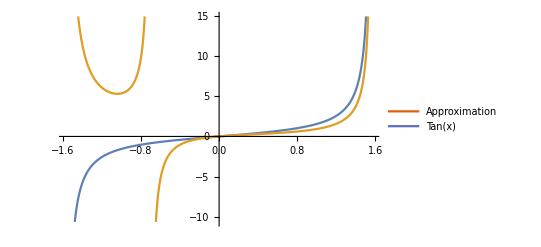

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],(x + x ^3/3)/((1 - 4 / Pi^2 * x ^2)*(1 + x * (1 + Pi^2/12 - 4/Pi^2) ))},{x,-Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```

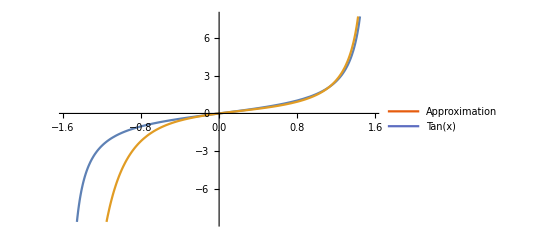

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
leg=LineLegend[colors[[;;2]],{"Approximation","Tan(x)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
p2=Plot[{Tan[x],(x + x^3/3)/((1 - 4 / Pi^2 * x ^2)*(1 + x * ( Pi^2 + Pi^4/12 - 8)/(2 * Pi^2) ))},{x,-Pi/2,Pi/2},PlotLegends->leg,ImageSize->400]
```